-Graphics-

Podpořeno z projektu OPEN UNI - zlepšení otevřenosti a atraktivnosti studia na SU, CZ .02 .2 .69/0.0/0.0/18 _ 056/0013364.

# Second order pressure corrections to epicyclic frequency modes in non-slender tori around neutron stars

Based on the code written by  Straub & Sramkova, CQG, 2009 with corrections made by Horák, J., Straub, O., Šrámková, E., Goluchová, K., & Török, G. 2017, in RAGtime 17-19: Workshops on Black Holes and Neutron Stars, 47–59.

To describe the geometry around a neutron star we use the Hartle-Thorne metric (Hartle, J. B. & Thorne, K. S. 1968, APJ, 153, 807) and we use relations derived by Abramowicz, M . A ., Almergren, G . J . E ., Kluźniak, W ., & Thampan, A . V . 2003, gr qc, gr - qc/0312070.

## 1. The geometry

### The Hartle - Thorne metric

#### Metric coefficients

```mathematica
M=1;

F1=-(8M r^4 (r-2M))^(-1)(u^2(48M^6-8M^5r-24M^4r^2-30M^3r^3-60M^2r^4+135M r^5-45r^6)+(r-M)(16M^5+8M^4r-10M^2r^3-30M r^4+15r^5))+A1;
F2=(8M r(r-2M))^(-1)5(3u^2-1)(r-M)(2M^2+6M r-3r^2)-A1;
G1=(8M r^4 (r-2M))^(-1)(L-72M^5r-3u^2(L-56M^5r))-A1;
L=80M^6+8M^4r^2+10M^3r^3+20M^2r^4-45M r^5+15r^6;
H1=(8M r^4)^(-1)(1-3u^2)(16M^5+8M^4r-10M^2r^3+15M r^4+15r^5)+A2;
H2=(8M r)^(-1)5(1-3u^2)(2M^2-3M r-3r^2)-A2;
A1=15r(r-2M)(1-3u^2)/(16M^2) Log[r/(r-2M)];
A2 =15(r^2-2M^2)(3u^2-1)/(16M^2) Log[r/(r-2M)];
u = Cos[h];

metric=Array[g,{4,4}];
g[1,1]=-(1-2M/r)(1+j^2F1+q F2); g[1,2]=0; g[1,3]=0; g[1,4]=-2M^2/r j  (1-u^2);
g[2,1]=0; g[2,2]=(1-2M/r)^(-1)(1+j^2G1-q F2); g[2,3]=0; g[2,4]=0;
g[3,1]=0; g[3,2]=0; g[3,3]=r^2(1+j^2H1+q H2); g[3,4]=0;
g[4,1]=g[1,4]; g[4,2]=0; g[4,3]=0; g[4,4]=r^2(1-u^2)(1+j^2H1+q H2);

inversemetric=Inverse[metric];

gtt=Simplify[metric[[1,1]]];
gtp=Simplify[metric[[1,4]]];
grr=Simplify[metric[[2,2]]];
ghh=Simplify[metric[[3,3]]];
gpp=Simplify[metric[[4,4]]];

gTT=Simplify[inversemetric[[1,1]]]; 
gTP=Simplify[inversemetric[[1,4]]];
gRR=Simplify[inversemetric[[2,2]]];
gHH=Simplify[inversemetric[[3,3]]];
gPP=Simplify[inversemetric[[4,4]]];
```

#### Metric derivatives

```mathematica
gRRdr=Simplify[D[gRR,r]];
gHHdh=Simplify[D[gHH,h]];
```

#### The determinant and derivatives

```mathematica
detg=Simplify[Det[metric],Assumptions->{r>0,Sin[h]>0}];
```

```mathematica
sqG=Sqrt[-detg];

(* derivative of sqrt of -g *)
drg=D[sqG,r];
dhg=D[sqG,h];
```

#### The orbital angular velocity Ω

```mathematica
Ω=-(gtp + l0 gtt)/(gpp + l0 gtp);
```

The specific angular momentum taken at the torus centre is l_0 = const throughout the torus

#### The 4 - velocity

```mathematica
uT=Factor[1/Sqrt[(-gtt-2 Ω gtp-Ω^2 gpp)]]; 
uP=Factor[uT Ω];
```

```mathematica
ut=Factor[uT (gtt+Ω   gtp)];      (* specific energy *)
up= Factor[uT (gtp + Ω gpp)];     (* specific angular momentum *)
```

#### The effective potential

```mathematica
Ueff=Simplify[(gTT-2 gTP ell + gPP ell^2)] ;
```

#### The Keplerian angular momentum

```mathematica
L0L=(M^(1/2)r^(3/2))/(r-2M);
F1L=(16M^2r^4(r-2M)^2)^(-1)(96M^8-112M^7r-8M^6r^2-48M^5r^3+42M^4r^4+220M^3r^5-260M^2r^6+105M r^7-15r^8)+A;
F2L=(16M^2r(r-2M))^(-1)5(6M^4-22M^2r^2+15M r^3-3r^4)+A;
A=((15)/(32M^3))(2M^3+4M^2r-4M r^2+r^3)Log[r/(r-2M)];

Lkepler1=L0L(1-j((M^(3/2)(3r-4M))/(r^(3/2)(r-2M)))+j^2  F1L-q F2L);
```

#### The Keplerian angular velocity

```mathematica
F1om=(48M^7-80M^6r+4M^5r^2-18M^4r^3+40M^3r^4+10M^2r^5+15M r^6-15r^7)(16M^2r^4(r-2M))^(-1)+Aom;
F2om=(5(6M^4-8M^3r-2M^2r^2-3M r^3+3r^4)/(16M^2r(r-2M)))-Aom;
Aom=(15(r^3-2M^3)/(32M^3))Log[r/(r-2M)];

ΩK=(M^(1/2)/r^(3/2))(1-j(M^(3/2)/r^(3/2))+j^2 F1om+q F2om);
```

### The radial and vertical epicyclic frequencies of a test particle

```mathematica
F1r=((6M^(3/2)(r+2M))/(r^(3/2)(r-6M)));
F2r=(8M^2r^4(r-2M)(r-6M))^(-1)(384M^8-720M^7r-112M^6r^2-76M^5r^3-138M^4r^4-130M^3r^5+635M^2r^6-375M r^7+60r^8)+Ar;
F3r=((5(48M^5+30M^4r+26M^3r^2-127M^2r^3+75M r^4-12r^5))/(8M^2r(r-2M)(r-6M)))-Ar;
Ar=((15r(r-2M)(2M^2+13M r-4r^2))/(16M^3(r-6M)))Log[r/(r-2M)];
rad=Sqrt[M(r-6M)r^(-4)(1+j F1r-j^2 F2r -q F3r)];
```

```mathematica
G1v=6M^(3/2)/r^(3/2);
G2v=(8M^2r^4(r-2M))^(-1)(48M^7-224M^6r+28M^5r^2+6M^4r^3-170M^3r^4+295M^2r^5-165M r^6+30r^7)-Bv;
G3v=((5(6M^4+34M^3r-59M^2r^2+33M r^3-6r^4))/(8M^2r(r-2M)))+Bv;
Bv=((15(2r-M)(r-2M)^2)/16M^3)Log[r/(r-2M)];
ver=Sqrt[M r^(-3)(1-j G1v+j^2 G2v +q G3v)];
```

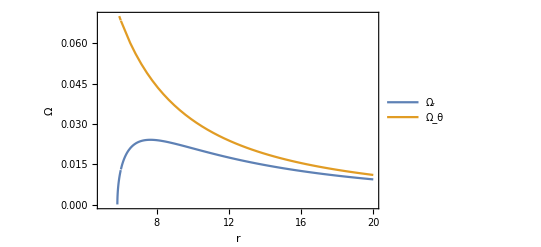

```mathematica
j=0.3; q=8j^2; Plot[{rad,ver},{r,5,20},PlotRange->{{5,20},{0,0.07}},Frame->True,Axes->False,FrameLabel->{"r","Ω"},LabelStyle->Directive[20,FontFamily->"Times New Roman"],PlotLegends->{Subscript["Ω","r"],Subscript["Ω","θ"]}]
Clear[j,q]
```

### Some interesting orbits

#### The innermost stable circular orbit

```mathematica
rms=6M(1-j((2/3)Sqrt[2/3])+j^2((251647/2592)-240Log[3/2])+q((-9325/96)+240Log[3/2]));
```

```mathematica
numrms:=r/.FindRoot[rad^2==0,{r,rms}]
```

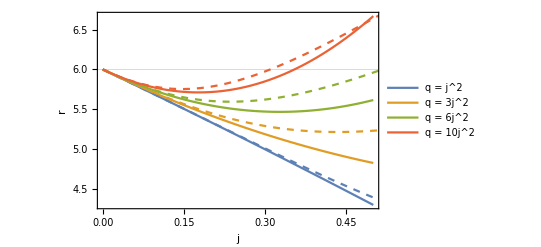

```mathematica
q=j^2; orbit1=Table[{j,numrms},{j,0,0.7,0.01}];  q=3j^2; orbit2=Table[{j,numrms},{j,0,0.7,0.01}]; q=6j^2; orbit3=Table[{j,numrms},{j,0,0.7,0.01}];  q=10j^2; orbit4=Table[{j,numrms},{j,0,0.7,0.01}]; Clear[j,q];
Show[Plot[{rms/.q->1j^2,rms/.q->3j^2,rms/.q->6j^2,rms/.q->10j^2},{j,0,0.5},PlotStyle->{Line},LabelStyle->Directive[20,FontFamily->"Times New Roman"],GridLines->{None,{6}},Frame->True,Axes->False,FrameLabel->{"j","r"},PlotLegends->{"q = j^2","q = 3j^2","q = 6j^2","q = 10j^2"}],ListLinePlot[{orbit1,orbit2,orbit3,orbit4},PlotStyle->{Dashed}]]
```

#### Marginally bound circular orbit

```mathematica
rmb=4M(1-j(1/2)-j^2((8047/256)-45Log[2])+q((1005/32)-45Log[2]));
```

```mathematica
numrmb:=If[j≥0, ftest[r0_]=ut0+1; count=0; countvalve=100; epsilon=0.000001; a=rmb-0.1; b=rms;  d=0.5(a+b); 
While[Abs[Chop[ftest[d]]]>epsilon,  count=count+1; d=0.5(a+b); If[Chop[ftest[d]]*Chop[ftest[a]]<0,b=d,a=d]; If[count>countvalve,{Print["error"],Break[]}]];  nrmb=d; Clear[a,b,d,ftest,count]; nrmb]
```

#### NS surface

```mathematica
qstar=Piecewise[{{qa1 qx + qa0,qx>qx0},{qb (qx-1)^2+1,qx<=qx0}}];
qb=qa1^2/(4(-qa1-qa0+1));
qx0=2(1-qa0)/qa1-1;
qa1=3.64;qa0=-5.3;qx=qr/2;
```

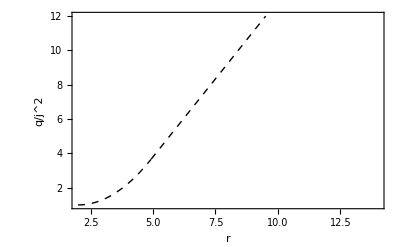

```mathematica
st=Plot[qstar,{qr,2,14},PlotRange->{{2,14},{1,12}},Frame->True,Axes->False,FrameLabel->{"r","q/j^2"},PlotStyle->{Black,Dashed,Thick}]
```

```mathematica
qstab=Table[{qstar,qr},{qr,2,9,0.1}];
rstar=Interpolation[qstab];
```

## 2. The relativistic Papaloizou-Pringle equation

### The coordinate transform r ---> x β, θ ---> y β

definition of the torus centre in terms of the expansion parameter β
for β = 0 we get the slender torus limit

```mathematica
B2 = β^2r0^2 A0^2 Ω0^2 /2;
```

```mathematica
rx=x β r0/Sqrt[grr0]+r0;  (* this x is \bar{x} = x/β *)
hy=π/2-y β r0/Sqrt[ghh0];  (* this y is \bar{y} = y/β *)
```

#### The coordinate transform of terms with derivatives of W

```mathematica
(* components *)
drW=dxW Sqrt[grr0]/(β r0);
dhW=-dyW Sqrt[ghh0]/(β r0);

drrW=dxxW (Sqrt[grr0]/(β r0))^2;
dhhW=dyyW (-Sqrt[ghh0]/(β r0))^2;
```

### The function f(x,y) in 0th, 1st, and 2nd order

```mathematica
U[r0,π/2]=U0;
```

```mathematica
(* the exact expression of f(r,theta) after the coordinate transform with relativistic definition of speed of sound*)
ft=Simplify[1-(1-Sqrt[U[rx,hy]/U0])/B2];
fce =1-(1-ut0/ut)/B2;
```

```mathematica
(* Taylor expansion of f *)
ftexp=Series[ft,{β,0,2}]/.{Derivative[0,1][U][r0,π/2]->0,Derivative[1,0][U][r0,π/2]->0,Derivative[1,1][U][r0,π/2]->0,Derivative[0,3][U][r0,π/2]->0,Derivative[2,1][U][r0,π/2]->0,Derivative[1,3][U][r0,π/2]->0,Derivative[3,1][U][r0,π/2]->0};
```

```mathematica
ft0=Simplify[SeriesCoefficient[ftexp,0]];
ft1=Simplify[SeriesCoefficient[ftexp,1]];
ft2=Simplify[SeriesCoefficient[ftexp,2]];
```

### Taylor series in β

#### Preliminary expansion in β : metric, determinant

```mathematica
TT=gTT0+gTT1 β+gTT2 β^2;
TP=gTP0+gTP1 β+gTP2 β^2;
RR=gRR0+gRR1 β+gRR2 β^2;
HH=gHH0+gHH1 β+gHH2 β^2;
PP=gPP0+gPP1 β+gPP2 β^2;
```

```mathematica
drgRR=drgRR0+drgRR1 β +drgRR2 β^2;
dhgHH=0+dhgHH1 β +dhgHH2 β^2;
```

```mathematica
SqG=SqG0+SqG1 β +SqG2 β^2;
```

```mathematica
drSqG=drSqG0 +drSqG1 β + drSqG2 β^2;
dhSqG=0 +dhSqG1 β + dhSqG2 β^2;
```

#### Preliminary expansion in β : f

```mathematica
f=f0+f1 β+f2 β^2;
```

#### Preliminary expansion in β : d f

```mathematica
dxf=dxf0+β dxf1+β^2 dxf2;
dyf=dyf0+β dyf1+β^2 dyf2;
```

```mathematica
drf=dxf grr0^(1/2)/(β r0);
dhf=-dyf ghh0^(1/2)/(β r0);
```

#### Preliminary expansion in β : Eigenvalue

```mathematica
ω=ω0+ω1 β + ω2 β^2;     (* ω=ω/Ω0  *)
```

```mathematica
AA=1 + AA1 β + AA2 β^2;    (* AA = u^t/u^t(r0) *)
ΩΩ=1 + ΩΩ1 β + ΩΩ2 β^2;    (* ΩΩ = Ω/Ω0 *)

EE=E0 + EE1 β + EE2 β^2;  (* EE = u_t *)
```

```mathematica
EV=Series[-2 n AA^2(ω -m ΩΩ)^2,{β,0,2}];

EV0=Simplify[SeriesCoefficient[EV,0]];
EV1=Collect[Expand[SeriesCoefficient[EV,1]/.{ω1->0}],{AA1,ΩΩ1}];
EV2=Collect[Expand[SeriesCoefficient[EV,2]/.{ω1->0}],{AA1,AA2,ΩΩ1,ΩΩ2}];
```

### Expansion coefficients

#### metric

```mathematica
r=rx; h=hy;
```

```mathematica
gTT0=Simplify[gTT/.β->0];
gTT1=Simplify[D[gTT,β]/.β->0];
gTT2=Simplify[1/2D[gTT,{β,2}]/.β->0];

gTP0=Simplify[gTP/.β->0];
gTP1=Simplify[D[gTP,β]/.β->0];
gTP2=Simplify[1/2D[gTP,{β,2}]/.β->0];

gPP0=Simplify[gPP/.β->0];
gPP1=Simplify[D[gPP,β]/.β->0];
gPP2=Simplify[1/2D[gPP,{β,2}]/.β->0];

gRR0=Simplify[gRR/.β->0];
gRR1=Simplify[D[gRR,β]/.β->0];
gRR2=Simplify[1/2D[gRR,{β,2}]/.β->0];

gHH0=Simplify[gHH/.β->0];
gHH1=Simplify[D[gHH,β]/.β->0];
gHH2=Simplify[1/2D[gHH,{β,2}]/.β->0];
```

```mathematica
drgRR0=Simplify[gRRdr/.β->0];
drgRR1=Simplify[D[gRRdr,β]/.β->0];
drgRR2=Simplify[1/2D[gRRdr,{β,2}]/.β->0];

dhgHH0=Simplify[gHHdh/.β->0];
dhgHH1=Simplify[D[gHHdh,β]/.β->0];
dhgHH2=Simplify[1/2D[gHHdh,{β,2}]/.β->0];
```

#### determinant

```mathematica
SqG0=Simplify[sqG/.β->0];
SqG1=Simplify[D[sqG,β]/.β->0];
SqG2=Collect[1/2D[sqG,{β,2}]/.β->0,{x,y}];
```

```mathematica
drSqG0=Simplify[drg/.β->0];
drSqG1=Collect[D[drg,β]/.β->0,x];
drSqG2=Collect[1/2D[drg,{β,2}]/.β->0,y];
```

```mathematica
dhSqG0=Simplify[dhg/.β->0];
dhSqG1=Collect[D[dhg,β]/.β->0,y];
dhSqG2=Collect[1/2D[dhg,{β,2}]/.β->0,{x,y}];
```

#### f

```mathematica
f0=ff00+ff0xx x^2+ff0yy y^2;
f1=ff1xxx x^3+ff1xyy x y^2;
f2=ff2xxxx x^4+ff2xx x^2+ ff2xxyy x^2 y^2+ff2yy y^2 +ff2yyyy y^4;
(* coefficients of f are defined later *)
```

```mathematica
dxf0=D[f0,x];
dyf0=D[f0,y];

dxf1=D[f1,x];
dyf1=D[f1,y];

dxf2=D[f2,x]; 
dyf2=D[f2,y];
```

#### A and Ω

```mathematica
AA0=1;
AA1=A1x x;
AA2=A2x x^2 + A2y y^2; 

ΩΩ0=1;
ΩΩ1=Ω1x x;
ΩΩ2=Ω2x x^2 + Ω2y y^2;

EE0=E0;
EE1=EE1x x;
EE2=EE2x x^2 + EE2y y^2; 

(* we know this shape from expanding the coord. transformed expressions 
ΩΩ = Ω(x,y) and AA = uT(x,y)  - see below *)
```

```mathematica
Clear[r,h]
```

### Expansion of the 9 individual terms in the L-operator

```mathematica
(* complete expanded L-operator with corrections *)
(*LW=Term1+Term2+Term3+Term4+Term5+Term6+Term7+Term8+Term9;*)
```

```mathematica
T1= β^2 r0^2 1/SqG * drSqG*RR * f/(B2 f+1-B2) * drW  /AA;
T2=β^2 r0^2 drgRR * f/(B2 f+1-B2) * drW /AA;
T3=Simplify[β^2 r0^2  RR *(n drf/(B2 f+1-B2) /AA-B2 f *drf/(B2 f+1-B2)^2) drW /AA];
T4= β^2 r0^2 RR f/(B2 f+1-B2) drrW /AA;

T5=β^2 r0^2 1/SqG * dhSqG*HH * f/(B2 f+1-B2) * dhW /AA;
T6=β^2 r0^2 dhgHH * f/(B2 f+1-B2) * dhW /AA;
T7=Simplify[β^2 r0^2 HH*(n dhf/(B2 f+1-B2) /AA-B2 f *dhf/(B2 f+1-B2)^2) * dhW /AA];
T8=β^2 r0^2 HH * f/(B2 f+1-B2) * dhhW /AA;

T9=β^2 r0^2 *(l0 ω Ω0 - m)^2(ΩΩ Ω0 TP - PP)/(1 - ΩΩ Ω0 l0)* f/(B2 f+1-B2) W /AA;
```

```mathematica
T10=T1/.β->0; 
dT1=D[T1,β]; 
T11=dT1/.β->0; 
T12=D[dT1,β]/.β->0;

T20=T2/.β->0;
dT2=D[T2,β];
T21=dT2/.β->0;
T22=D[dT2,β]/.β->0;

T30=T3/.β->0;
dT3=D[T3,β];
T31=dT3/.β->0;
T32=D[dT3,β]/.β->0;

T40=T4/.β->0;
dT4=D[T4,β];
T41=dT4/.β->0;
T42=D[dT4,β]/.β->0;

T50=T5/.β->0;
dT5=D[T5,β];
T51=dT5/.β->0;
T52=D[dT5,β]/.β->0;

T60=T6/.β->0;
dT6=D[T6,β];
T61=dT6/.β->0;
T62=D[dT6,β]/.β->0;

T70=T7/.β->0;
dT7=D[T7,β];
T71=dT7/.β->0;
T72=D[dT7,β]/.β->0;

T80=T8/.β->0;
dT8=D[T8,β];
T81=dT8/.β->0;
T82=D[dT8,β]/.β->0;

T90=T9/.β->0;
dT9=D[T9,β];
T91=dT9/.β->0;
T92=D[dT9,β]/.β->0;
```

```mathematica
(* 0th, 1st, and 2nd order of the L-operator *)
L0W=T10+T20+T30+T40+T50+T60+T70+T80+T90;
L1W=Collect[T11+T21+T31+T41+T51+T61+T71+T81+T91,{dxW,dyW,dxxW,dyyW},Simplify];
L2W=1/2Collect[T12+T22+T32+T42+T52+T62+T72+T82+T92,{W,dxW,dyW,dxxW,dyyW}];
```

### *Torus centre r0

```mathematica
uT0=Simplify[uT/.{r->r0,h->Pi/2}] ;   (* = A0 LATER *)
```

```mathematica
ut0=uT0 (gtt0+Ω0 gtp0);     (* specific energy *)
up0= uT0 (gtp0 + Ω0 gpp0); (* specific angular momentum *)
```

```mathematica
(* metric components at the torus centre r=r_0 and theta = π/2 *)
r=r0; h=π/2;
gtt0=Cancel[gtt]; 
gtp0=Cancel[gtp];
grr0=Cancel[grr]; 
ghh0=Cancel[ghh]; 
gpp0=Cancel[gpp]; 
r=.;  h=.;
```

```mathematica
U0=-1/E0^2;
```

### Finding the eigenfunctions from the 0th order PP equation

σσ= σ^2

```mathematica
pp=ff[x,y](D[W[x,y],x,x]+D[W[x,y],y,y])+n(D[ff[x,y],x]D[W[x,y],x]+D[ff[x,y],y]D[W[x,y],y])+2n σσ W[x,y];

pp0=pp/.ff->Function[{x,y},1-ωR^2x^2-ωH^2y^2];
```

```mathematica
(* 1st, i.e. radial epicyclic mode, W=x *)
W1Mode=pp0/.W->Function[{x,y},x]//Simplify;
Px=Coefficient[W1Mode,x];
Sigma1coeff=Solve[Px==0,σσ]//Flatten;
W1coeff=Sigma1coeff;
```

```mathematica
(* 2nd, i.e. vertical epicyclic mode, W=y *)
W2Mode=pp0/.W->Function[{x,y},y]//Simplify;
Py=Coefficient[W2Mode,y];
Sigma2coeff=Solve[Py==0,σσ]//Flatten;
W2coeff=Sigma2coeff;
```

```mathematica
(* 3rd, i.e. X mode, W=xy *)
W3Mode=pp0/.W->Function[{x,y},x y]//Simplify;
Pxy=Coefficient[W3Mode,x y];
Sigma3coeff=Solve[Pxy==0,σσ]//Flatten;
W3coeff=Sigma3coeff;
```

```mathematica
(* 4th and 5th, i.e. plus and breathing mode, W=(1+aa x^2 + bb y^2) *)
W4Mode=pp0/.W->Function[{x,y},(1+aa x^2 + bb y^2)]//Simplify;

Pxx=Coefficient[W4Mode,x^2 ];
Pyy=Coefficient[W4Mode,y^2];
P0=Factor[W4Mode-Pxx x^2 - Pyy  y^2];

AB4coeff=Solve[Pxx==0&&P0==0,{aa,bb}]//Simplify//Flatten;
Sigma4coeff=Solve[Pyy==0//.AB4coeff,σσ]//FullSimplify;

W4coeff=Union[AB4coeff,Sigma4coeff[[2]]];
W5coeff=Union[AB4coeff,Sigma4coeff[[3]]];
```

## 3. Eigenfunctions

```mathematica
W0=a0;

W1=a1 x;
W2=a2 y;
W3=a3 x y;

W4=a4 (1+aa x^2 + bb y^2)//.AB4coeff/.{σσ->σ4^2}//Simplify;
W5=a5 (1+aa x^2 + bb y^2)//.AB4coeff/.{σσ->σ5^2}//Simplify;
```

```mathematica
(* 4th eigenmode, coefficients of x and y terms *)
W40=(Expand[W4]/a4/. x -> 0)/. y -> 0;
W4xx=Factor[((Expand[W4]/a4/. y -> 0) -W40)/x^2];
W4yy=Factor[((W4/a4/. x -> 0) -W40)/y^2];

(* 5th eigenmode, coefficients of x and y terms *)
W50=(Expand[W5]/a5/. x -> 0)/. y -> 0;
W5xx=Factor[((Expand[W5]/a5/. y -> 0) -W50)/x^2];
W5yy=Factor[((W5/a5/. x -> 0) -W50)/y^2];
```

```mathematica
(* derivatives of the eigenmodes with respect to x and y *)
dxW0=D[W0,x]; dxxW0=D[W0,x,x]; dyW0=D[W0,y]; dyyW0=D[W0,y,y];
dxW1=D[W1,x]; dxxW1=D[W1,x,x]; dyW1=D[W1,y]; dyyW1=D[W1,y,y];
dxW2=D[W2,x]; dxxW2=D[W2,x,x]; dyW2=D[W2,y]; dyyW2=D[W2,y,y];
dxW3=D[W3,x]; dxxW3=D[W3,x,x]; dyW3=D[W3,y]; dyyW3=D[W3,y,y];
dxW4=D[W4,x]; dxxW4=D[W4,x,x]; dyW4=D[W4,y]; dyyW4=D[W4,y,y];
dxW5=D[W5,x]; dxxW5=D[W5,x,x]; dyW5=D[W5,y]; dyyW5=D[W5,y,y];
```

## 4. Inner Product for ALL modes j : L | W_j >

#### 1st order operator

```mathematica
(*
The following expressions are labeled with -x and -y suffixes according to which terms they are connected, e.g. 
L1W2xy is the coefficient that belongs to the term L1W2 = L1W2xy * xy 
(this notation simplifies the elliptical integrals below)
*)
```

```mathematica
dxW=dxW0; dyW=dyW0;dxxW=dxxW0; dyyW=dyyW0;

L1W0=L1W ;(* =0  *)
```

```mathematica
dxW=dxW1; dyW=dyW1;dxxW=dxxW1; dyyW=dyyW1;
L1W1=Collect[L1W,{x,y}];

L1W1xx=Coefficient[L1W,x,2];
L1W1yy=Coefficient[L1W,y,2];
L1W1J=CoefficientList[L1W1,x][[1]]/.y->0;
```

```mathematica
dxW=dxW2; dyW=dyW2;dxxW=dxxW2; dyyW=dyyW2;
L1W2=Collect[L1W,{x,y}];

L1W2xy=Coefficient[L1W2,x y];
```

```mathematica
dxW=dxW3; dyW=dyW3;dxxW=dxxW3; dyyW=dyyW3;

L1W3=Collect[L1W,{x,y}];

L1W3xxy=Coefficient[L1W3,x^2y];
L1W3yyy=Coefficient[L1W3,y^3];
L1W3y=Coefficient[L1W3,y]/.x^2->0;
```

```mathematica
dxW=dxW4; dyW=dyW4;dxxW=dxxW4; dyyW=dyyW4;

L1W4=Collect[L1W,{x,y}];

L1W4xxx=Coefficient[L1W4,x^3];
L1W4xyy=Coefficient[L1W4,x y^2];
L1W4x=Coefficient[L1W4,x]/.y^2->0;
```

```mathematica
dxW=dxW5; dyW=dyW5;dxxW=dxxW5; dyyW=dyyW5;
L1W5=Collect[L1W,{x,y}];

L1W5xxx=Coefficient[L1W5,x^3];
L1W5xyy=Coefficient[L1W5,x y^2];
L1W5x=Coefficient[L1W5,x]/.y^2->0;
```

#### 2nd order operator

```mathematica
W=W0; dxW=dxW0; dyW=dyW0;dxxW=dxxW0; dyyW=dyyW0; ω0=ω00;

L2W0=Collect[L2W,{x,y}];

L2W0xx=Coefficient[L2W0,x^2];
L2W0yy=Coefficient[L2W0,y^2];
L2W0J=CoefficientList[L2W0,x][[1]]/.y->0;
```

```mathematica
W=W1; dxW=dxW1; dyW=dyW1;dxxW=dxxW1; dyyW=dyyW1; ω0=ω01;

L2W1=Collect[L2W,{x,y}];     

L2W1x=Coefficient[L2W1,x]/.y->0 ;
L2W1xyy=Coefficient[L2W1,x y^2];
L2W1xxx=Coefficient[L2W1,x^3];
```

```mathematica
W=W2; dxW=dxW2; dyW=dyW2;dxxW=dxxW2; dyyW=dyyW2;  ω0=ω02;

L2W2=Collect[L2W,{x,y}];

L2W2y=Coefficient[L2W2,y]/.x->0;
L2W2yyy=Coefficient[L2W2,y^3];
L2W2xxy=Coefficient[L2W2,x^2 y];
```

## 5. Mode Coefficients and Eigenfrequencies: a_i and σ_i

### finding the normalisation a_i of W from the inner product <W|W> = 1 (* intensive step *)

```mathematica
x=r Cos[h]/ωR;
y=r Sin[h]/ωH;
```

```mathematica
res0=Simplify[a02/.Last[Solve[(Integrate[(1-r^2)^(n-1) 1/ωR*1/ωH r * W0^2,{r,0,1},{h,0,2 π}, Assumptions-> n>0]/.a0^2-> a02)==1,a02]]];
```

```mathematica
res1=Simplify[a12/.Last[Solve[(Integrate[(1-r^2)^(n-1) 1/ωR*1/ωH r * W1^2,{r,0,1},{h,0,2 π}, Assumptions-> n>0]/.a1^2-> a12)==1,a12]]];
```

```mathematica
res2=Simplify[a22/.Last[Solve[(Integrate[(1-r^2)^(n-1) 1/ωR*1/ωH r * W2^2,{r,0,1},{h,0,2 π}, Assumptions-> n>0]/.a2^2-> a22)==1,a22]]];
```

```mathematica
res3=Simplify[a32/.Last[Solve[(Integrate[(1-r^2)^(n-1) 1/ωR*1/ωH r * W3^2,{r,0,1},{h,0,2 π}, Assumptions-> n>0]/.a3^2-> a32)==1,a32]]];
```

```mathematica
res4=Factor[a42/.Last[Solve[(Integrate[(1-r^2)^(n-1) 1/ωR*1/ωH r * W4^2,{r,0,1},{h,0,2 π}, Assumptions-> n>0]/.a4^2-> a42)==1,a42]]];
```

```mathematica
res5=Factor[a52/.Last[Solve[(Integrate[(1-r^2)^(n-1) 1/ωR*1/ωH r * W5^2,{r,0,1},{h,0,2 π}, Assumptions-> n>0]/.a5^2-> a52)==1,a52]]];
```

```mathematica
x=.; y=.;
```

### results for a_i

```mathematica
a0= Sqrt[res0];
a1= Sqrt[res1];
a2=Sqrt[res2];
a3=Sqrt[res3];
a4=Sqrt[res4];
a5=Sqrt[res5];
```

### eigenfrequencies σ_i

```mathematica
σ0=0;
σ1=Simplify[Sqrt[σσ/.W1coeff],Assumptions->ωR>0];
σ2=Simplify[Sqrt[σσ/.W2coeff],Assumptions->ωH>0];
σ3=Simplify[Sqrt[σσ/.W3coeff]];
σ4=Simplify[Sqrt[σσ/.W4coeff]];
σ5=Simplify[Sqrt[σσ/.W5coeff]];
```

## 6. Calculating the various INNER PRODUCTS: <W|L|W>

### Integrals over ellipses

"INTEGRALS OVER ANY KIND OF ODD XY-TERM EQUALS ZERO";

"e.g.:   XXXX = INTEGRAL OVER ANY TERM CONTAINING X^4, I.E. X*X^3 OR X^2*X^2 ETC"; 

"JJ DEFINES THE INTEGRAL OVER TERMS CONTAINING NEITHER X NOR Y";

```mathematica
x=r Cos[h]/ωR;
y=r Sin[h]/ωH;
```

```mathematica
JJ=Integrate[(1-r^2)^(n-1) 1/ωR*1/ωH r * 1,{r,0,1},{h,0,2 π}, Assumptions-> n>0];

xx=Integrate[(1-r^2)^(n-1) 1/ωR*1/ωH r * x^2,{r,0,1},{h,0,2 π}, Assumptions-> n>0];
yy=Integrate[(1-r^2)^(n-1) 1/ωR*1/ωH r * y^2,{r,0,1},{h,0,2 π}, Assumptions-> n>0];

xxxx=Factor[3 π/(4 n (n+1) (n+2) ωR^5 ωH^1)];
yyyy=Factor[3 π/(4 n (n+1) (n+2) ωR^1 ωH^5)];
xxyy=Factor[1 π/(4 n (n+1) (n+2)ωR^3 ωH^3 )];
```

```mathematica
x=.; y=.;
```

### 1st order

#### L1

```mathematica
(* NB these are all 0 becasue L1W0 = 0 *)
W1L1W0=W1 L1W0;
W1L1W4=a1 (L1W4x xx + L1W4xyy xxyy + L1W4xxx xxxx);
W1L1W5=a1 (L1W5x xx + L1W5xyy xxyy + L1W5xxx xxxx);
```

```mathematica
W2L1W3=a2 (L1W3y yy + L1W3xxy xxyy + L1W3yyy yyyy) ;
```

```mathematica
(* NB L1W1 = L1W1J + L1W1xx + L1W1yy ---  all modes with odd x,y are 0 *)
W0L1W1=a0 (L1W1J JJ + L1W1xx xx + L1W1yy yy);
W1L1W1=0;W2L1W1=0;W3L1W1=0;
W4L1W1=a4 (W40 (L1W1J JJ + L1W1xx xx + L1W1yy yy) + W4xx (L1W1J xx + L1W1xx xxxx + L1W1yy xxyy) + W4yy (L1W1J yy + L1W1xx xxyy + L1W1yy yyyy));
W5L1W1=a5 (W50 (L1W1J JJ + L1W1xx xx + L1W1yy yy) + W5xx (L1W1J xx + L1W1xx xxxx +  L1W1yy xxyy) + W5yy (L1W1J yy +  L1W1xx xxyy +  L1W1yy yyyy));
```

```mathematica
(* NB L1W2 = L1W2xy---  all modes with even/odd x,y are 0, only those with x*y go *)
W0L1W2=0; W1L1W2=0; W2L1W2=0;
W3L1W2=a3 L1W2xy xxyy;
```

#### Ω1

```mathematica
W1Ω1W0=Factor[a1 a0 Ω1x  xx ];
```

```mathematica
W0Ω1W1=a1 a0 Ω1x  xx; 
W1Ω1W1=W2Ω1W1=W3Ω1W1=0;
W4Ω1W1=a1 a4 Ω1x (W40 xx + W4xx xxxx + W4yy xxyy); 
W5Ω1W1=a1 a5 Ω1x (W50 xx + W5xx xxxx + W5yy xxyy);
```

```mathematica
W0Ω1W2=W1Ω1W2=W2Ω1W2=0;
W3Ω1W2=a2 a3 Ω1x  xxyy;
```

```mathematica
W1Ω1W4=W4Ω1W1;
W1Ω1W5=W5Ω1W1;
```

```mathematica
W2Ω1W3=W3Ω1W2;
```

### 2nd order

#### L2

```mathematica
(* L2W1xyy + L2W1x + L2W1xxx *)
W1L2W1=a1 (L2W1x xx + L2W1xyy xxyy + L2W1xxx xxxx);
```

```mathematica
(* L2W2yyy + L2W2xxy + L2W2y *)
W2L2W2=a2 (L2W2yyy yyyy+L2W2xxy xxyy+L2W2y yy);
```

#### Ω1^2

```mathematica
(* < W ￿| Ω1^2 ￿| W > *)
W1Ω12W1=Factor[a1^2 Ω1x^2 xxxx];
W2Ω12W2=Factor[a2^2 Ω1x^2 xxyy];
```

#### Ω2

```mathematica
W1Ω2W1=Factor[a1^2 (Ω2x xxxx + Ω2y xxyy)];
W2Ω2W2=Factor[a2^2 (Ω2x xxyy + Ω2y yyyy)];
```

## 7. bij (for each mode i of interest)

```mathematica
b10=(W0L1W1-4 n m σ1 W0Ω1W1)/(2 n(σ0^2-σ1^2));   
b14=(W4L1W1-4 n m σ1 W4Ω1W1)/(2 n(σ4^2-σ1^2));
b15=(W5L1W1-4 n m σ1 W5Ω1W1)/(2 n(σ5^2-σ1^2));
```

```mathematica
b23=(W3L1W2-4 n m σ2 W3Ω1W2)/(2 n(σ3^2-σ2^2));
```

## 8. Taylor Series Part 2: expansion of Ω, A and f in β

NOTE: do NOT execute this step earlier as the use of the resulting coefficients SLOWS down the above (main) calculation otherwise

1 REFERS TO THE 1ST ORDER EXPANSION TERM, 
2 REFERS TO THE 2ND ORDER EXPANSION TERM

### l_0, A_0, Ω_0, values at the pressure maximum r_0

```mathematica
r=r0; h=Pi/2;

l0=ell=Lkepler1;
Ω0=Ω;
A0=Collect[uT0,{j,q}];
E0=Collect[-ut0,{j,q}];

Clear[r,h];
```

```mathematica
kΩ0=Ω0/.{j->0,q->0};
jΩ0=D[Ω0,j]/.{j->0,q->0};
j2Ω0=D[Ω0,{j,2}]/.{j->0,q->0};
qΩ0=D[Ω0,q]/.{j->0,q->0};
Ω0=kΩ0 +j jΩ0+1/2j^2j2Ω0+q qΩ0;
```

### f(r,θ) coefficients in 0th, 1st, and 2nd order

```mathematica
(* the non-zero derivatives of the potential U_eff *)

Derivative[2,0][U][r0,π/2]=D[Ueff,r,r]/.{r->r0,h->Pi/2};
Derivative[0,2][U][r0,π/2]=D[Ueff,h,h]/.{r->r0,h->Pi/2};

Derivative[3,0][U][r0,π/2]=D[Ueff,r,r,r]/.{r->r0,h->Pi/2};
Derivative[1,2][U][r0,π/2]=D[Ueff,h,h,r]/.{r->r0,h->Pi/2};

Derivative[0,4][U][r0,π/2]=D[Ueff,h,h,h,h]/.{r->r0,h->Pi/2};
Derivative[4,0][U][r0,π/2]=D[Ueff,r,r,r,r]/.{r->r0,h->Pi/2};
Derivative[2,2][U][r0,π/2]=D[Ueff,r,r,h,h]/.{r->r0,h->Pi/2};
```

```mathematica
ff00=Coefficient[Coefficient[ft0,x,0],y,0];  
ff0xx=Coefficient[ft0,x,2];
ff0yy=Coefficient[ft0,y,2];

(* 0th order f -> OK *)
```

```mathematica
ff1xxx=Coefficient[ft1,x,3];
ff1xyy=Coefficient[ft1,x y^2];
```

```mathematica
ff2xxxx=Coefficient[ft2,x,4];
ff2yyyy=Coefficient[ft2,y,4];
ff2xx=Coefficient[ft2,x,2]/.y->0;
ff2yy=Coefficient[ft2,y,2]/.x->0;
ff2xxyy=Coefficient[ft2,x^2 y^2];
```

### COORDINATE TRANSFORM of ut and uT

```mathematica
uTt=uT/.{r->rx,h->hy} ;
(* after coordinate transform at r=r0, l0=lK(r0)   *)
```

```mathematica
utt=ut/.{r->rx,h->hy};(* after coordinate transform at r=r0 *)
upt=up/.{r->rx,h->hy};
```

### COORDINATE TRANSFORM of Ω and A

```mathematica
Ωt=Ω/.{r->rx,h->hy} ;
At=uTt;
```

### EXPANSION of Ω and A (i.e. u^t)

```mathematica
(* the following quantities depend, via Ω, on l_0 *)

Ωex=Series[Ωt/Ω0,{β,0,2}];
```

```mathematica
kA=At/A0/.β->0;
dA=D[At/A0,β];
bA=Collect[dA/.β->0,x];
b2A=1/2 Collect[D[dA,β]/.β->0,{x,y}];
```

```mathematica
Ω00=SeriesCoefficient[Ωex,0];  (* = ΩΩ0 *)
Ω1x=Coefficient[SeriesCoefficient[Ωex,1],x];
Ω2x=Coefficient[SeriesCoefficient[Ωex,2],x^2];
Ω2y=Coefficient[SeriesCoefficient[Ωex,2],y^2];
```

```mathematica
A00=kA;
A1x=Coefficient[bA,x];
A2x=Coefficient[b2A,x^2];
A2y=Coefficient[b2A,y^2];
```

## 9. The oscillation frequencies

```mathematica
n=3;
```

### The eigenfrequencies of each order

#### 0th order frequencies (ω_0i)

```mathematica
Clear[ωR,ωH]
```

```mathematica
ωR=Sqrt[-ff0xx];         (* this is omega - "bar" *)
ωH=Sqrt[-ff0yy];
```

```mathematica
kωR=Simplify[ωR^2/.{j->0,q->0}];
jωR=Simplify[D[ωR^2,j]/.{j->0,q->0}];
j2ωR=Simplify[D[ωR^2,{j,2}]/.{j->0,q->0}];
qωR=Simplify[D[ωR^2,q]/.{j->0,q->0}];
```

```mathematica
ωR=Sqrt[kωR+j jωR+1/2 j^2 j2ωR+q qωR];
```

```mathematica
kωH=Simplify[ωH^2/.{j->0,q->0}];
jωH=Simplify[D[ωH^2,j]/.{j->0,q->0}];
j2ωH=Simplify[D[ωH^2,{j,2}]/.{j->0,q->0}];
qωH=Simplify[D[ωH^2,q]/.{j->0,q->0}];
```

```mathematica
ωH=Sqrt[kωH+j jωH+1/2 j^2 j2ωH+q qωH];
```

```mathematica
(* 0th order modes *)
ω00=1+m;
ω01=ωR+m;  
ω02=ωH+m;
```

#### 1st order corrections (ω_1i)

```mathematica
ω11=-1/(4 n σ1)*(W1L1W1 -4 n m σ1 W1Ω1W1);
ω12=-1/(4 n σ2)*(W2L1W2-4 n m σ2 W2Ω1W2);
```

```mathematica
Factor[ω11]
Factor[ω12]
```

0

0

#### 2nd order corrections (ω_2i)

```mathematica
ω21=-1/(4n σ1) *((W1L2W1 + 2n m^2 W1Ω12W1 - 4n m σ1 W1Ω2W1) 
+ b10 (W1L1W0 - 4n m σ1 W1Ω1W0 )
+ b14 (W1L1W4 - 4n m σ1 W1Ω1W4 )
+ b15(W1L1W5 - 4n m σ1 W1Ω1W5 ));
```

```mathematica
ω22=-1/(4n σ2) *((W2L2W2 + 2n m^2 W2Ω12W2 - 4n m σ2 W2Ω2W2) 
+ b23(W2L1W3 - 4n m σ2 W2Ω1W3 ));
```

```mathematica
j=0;q=0;m=-1;
test=Simplify[ω22,Assumptions->{r0>2}]
Clear[j,q,m]
```

0

### Epicyclic frequencies of the 0th order

ν = R ω / 2π, where R is a factor that accounts for the source properties - M,c,G - defined below

#### Keplerian frequency

```mathematica
νK=Simplify[Ω0 R/2/π];
```

#### slender frequencies

```mathematica
kνR0=(ωR Ω0)^2/.{j->0,q->0};
jνR0=D[(ωR Ω0)^2,j]/.{j->0,q->0};
j2νR0=1/2D[(ωR Ω0)^2,{j,2}]/.{j->0,q->0};
qνR0=D[(ωR Ω0)^2,q]/.{j->0,q->0};

νR0=(Sqrt[kνR0+j jνR0+j^2 j2νR0+q qνR0]+m Ω0) R/2/π;
```

```mathematica
kνH0=(ωH Ω0)^2/.{j->0,q->0};
jνH0=D[(ωH Ω0)^2,j]/.{j->0,q->0};
j2νH0=1/2D[(ωH Ω0)^2,{j,2}]/.{j->0,q->0};
qνH0=D[(ωH Ω0)^2,q]/.{j->0,q->0};

νH0=(Sqrt[kνH0+j jνH0+j^2 j2νH0+q qνH0]+m Ω0) R/2/π;
```

### NON-SLENDER RESULT : epicyclic frequencies with 2nd order corrections

```mathematica
νR=νR0 +β^2 ω21 Ω0 R/2/π;
νH=νH0 +β^2 ω22 Ω0 R/2/π;
```

### cusp radius and β_max(r_0)

calculated from the intersection between the Keplerian angular momentum l_K and the l_0 = const.

```mathematica
Clear[r,j,q]
```

```mathematica
rcus=krcus( 1 + j jrcus + j^2 j2rcus + q qrcus);
```

```mathematica
resrcus=(Lkepler1/.r->rcus)-l0;
```

```mathematica
kresrcus= resrcus/.{j->0,q->0};
jresrcus=D[resrcus,j]/.{j->0,q->0};
j2resrcus=D[resrcus,{j,2}]/.{j->0,q->0};
qresrcus=D[resrcus,q]/.{j->0,q->0};
```

```mathematica
(*Reduce[kresrcus==0,krcus,Reals]*)
```

```mathematica
(*krc=Simplify[Solve[FullSimplify[kresrcus]==0,krcus]];*)
jrc=Simplify[Solve[FullSimplify[jresrcus]==0,jrcus]][[1]];
j2rc=Simplify[Solve[FullSimplify[j2resrcus]==0,j2rcus]][[1]];
qrc=Simplify[Solve[FullSimplify[qresrcus]==0,qrcus]][[1]];
```

```mathematica
rc=rcus/.qrc/.j2rc/.jrc;
```

```mathematica
krcus=(2(-1 r0+r0^2))/(-2+r0)^2+2 √((-3 r0^2+2 r0^3)/(-2+r0)^4);
```

```mathematica
maxrc:=r0/.FindRoot[rc-r0==0,{r0,rms}]
```

```mathematica
(*maxrc:=If[j≥0,ftest[r0_]=rc-r0;a=rmb;b=rms+1.5;count=0; epsilon=0.000001;countvalve=100;
While[Abs[ftest[b]-ftest[a]]>epsilon, d=(a+b)/2; If[ftest[a]ftest[d]<0,b=d,a=d]; count=count+1;If[count>countvalve,{Print["precision error"],Break[]}]]; cuspr=d; Clear[a,b,d]; cuspr]; *)
rcusp[rmx_]:=Piecewise[{{r0,r0≤rmx},{rc,r0>rmx}}];
```

Take the equipotential function f =  1 - 1/(n cs0^2) *(1 - E0/E)  and replace (n cs0^2) with 2/(β^2 r0^2 A^2 Ω0^2) . The maximum torus surface is given by self-crossing equipotential line, f = 0, crosses the equatorial plane at r = r_cusp = r_in. We solve f = 0 at r = r_cusp for β. This is to get for each combination of j, q and r0 the maximum possible "non-slenderness".

```mathematica
(* β-boundary gives for each r0 the maximum possible β *)
βmax2=2/(Ω0^2 A0^2 r0^2)  * (1-ut0/ut)/.r->rc/.h->Pi/2;
```

```mathematica
βmax:=Piecewise[{{0,r0≤maxrc},{Sqrt[βmax2],r0>maxrc}}];
```

### Boundary frequency ν_b

```mathematica
νbor=νR/.β^2->βmax2;    
νboh=νH/.β^2->βmax2;
(* because of approximation of rc β could be less than 0 *)
```

```mathematica
νcuspr:=Piecewise[{{νR0,r0≤maxrc},{νbor,r0>maxrc}}];
νcusph:=Piecewise[{{νH0,r0≤maxrc},{νboh,r0>maxrc}}];
(* exclude β < 0 *)
```

### r_max

calculated from the intersection between the Keplerian angular momentum l_K and the l_0 = const.

```mathematica
rmax:=If[j≥0, ftest[r0_]=Lkepler1-l0/.{r->numrmb,h->Pi/2}; count=0; countvalve=100; epsilon=0.000001; a=rms; b=20;  d=0.5(a+b); 
While[Abs[Chop[ftest[d]]]>epsilon,  count=count+1; d=0.5(a+b); If[Chop[ftest[d]]*Chop[ftest[a]]<0,b=d,a=d]; If[count>countvalve,{Print["error"],Break[]}]];  maxr=d; Clear[a,b,d,ftest,count]; maxr]
```

```mathematica
rinmax:=r/.FindRoot[ut+1/.h->Pi/2,{r,5},AccuracyGoal->3,PrecisionGoal->4]
βmaxim2:=2/(Ω0^2 A0^2 r0^2)  * (1-ut0/ut)/.r->rinmax/.h->Pi/2;
```

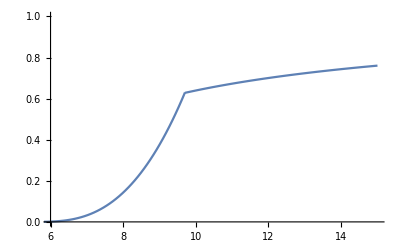

```mathematica
j=0.3;q=6j^2;rm=rmax;
Show[Plot[{βmax2},{r0,rms,rm},PlotRange->{{6,15},{0,1}}],Plot[{βmaxim2},{r0,rm,15}]]
Clear[j,q,r0]
```

## 10. Plots

### Shape of torus

```mathematica
j=0.3;q=5j^2;r0=7.4;Sqrt[βmax2]
funkce[r_,h_]= 1-(1-ut0/ut)/B2/.β->Sqrt[βmax2];
torus=Show[DensityPlot[funkce[Sqrt[x*x+y*y],ArcTan[y,x]] ,{x,rc,15},{y,-4,4},PlotRange->{{4,14},{-4,4}},RegionFunction->Function[{x,y},funkce[Sqrt[x*x+y*y],ArcTan[y,x]]≥0], AspectRatio->1,LabelStyle->{16,FontFamily->"Times"},ColorFunction->"Rainbow",MaxRecursion->10,FrameLabel->{"r sin θ","r cos θ"}],
ListPlot[{{r0,0}},PlotStyle->{Darker[Red],PointSize[Medium]}]]
Clear[j,q,r0]
```

0.278786

-Graphics-

### Radial axisymmetric oscillations

```mathematica
Clear[j,q,M,R]
```

```mathematica
c= 2.99792458 10^10 ;    (* speed of light given in [cm/s]  *)
G=6.67428 10^(-8) ;      (* gravitational constant in [cm^3/(g*s^2)] *)

Msun=1.98892 10^(33);    (*solar mass in [g]  *)                   
R=c^3/(G Msun) ;                         (* unit conversion *)
```

```mathematica
color={Black,RGBColor[0,0.1,1],RGBColor[0.2,0,0.8],RGBColor[0.5,0,0.5]}
```

{GrayLevel[0],RGBColor[0, 0.1, 1],RGBColor[0.2, 0, 0.8],RGBColor[0.5, 0, 0.5]}

```mathematica
r1=4.5;r2=15;
```

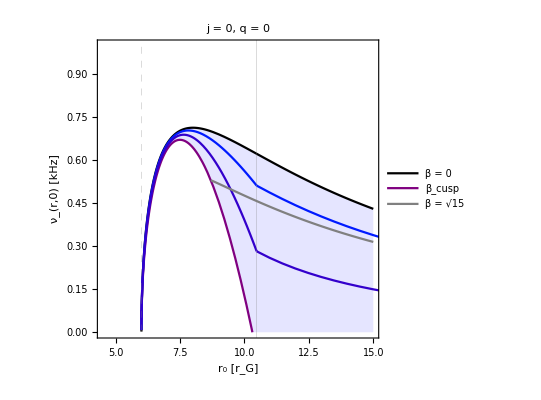

```mathematica
j=0;q=0;m=0; rm=rmax;
nur0j0q0b0=νR0/1000;
nur0j0q0b015=νR/1000/.{β^2->0.15};
nur0j0q0b04=νR/1000/.{β^2->0.4^2βmax2};
nur0j0q0b07=νR/1000/.{β^2->0.7^2βmax2}; 
nur0j0q0b1=νcuspr/1000;
fcebeta=2/(Ω0^2 A0^2 r0^2)  * (1-ut0/ut)/.{r->rc,h->Pi/2};
fbeta[r0_]=fcebeta-0.15;  abeta=rms; bbeta=rms+10;  cbeta=0.5(abeta+bbeta);countbeta=0; countvalve=100; epsilon=0.000001;
While[Abs[Chop[fbeta[cbeta]]]>epsilon, countbeta=countbeta+1; cbeta=0.5(abeta+bbeta); If[Chop[fbeta[cbeta]]*Chop[fbeta[abeta]]<0,bbeta=cbeta,abeta=cbeta]; If[countbeta>countvalve,{Print["error"],Break[]}]]; rb015=cbeta; Clear[abeta,bbeta,cbeta,countbeta,fbeta];
nur0j0q0b04b:=νR/1000/.{β^2->0.4^2βmaxim2};
nur0j0q0b07b:=νR/1000/.{β^2->0.7^2βmaxim2}; 
nur0j0q0b04tab=Table[{r0,nur0j0q0b04b},{r0,rm,r2+0.5,0.5}];
nur0j0q0b07tab=Table[{r0,nur0j0q0b07b},{r0,rm,r2+0.5,0.5}];
Clear[j,q,m]
rad0j0q0=Show[Plot[{nur0j0q0b0,nur0j0q0b1},{r0,r1,r2},Frame->True,Axes->False,PlotStyle->{color[[1]],color[[4]]},PlotRange->{{r1,r2},{0,1}},AspectRatio->1, Filling->{1->{2}},FillingStyle->Directive [Blue,Opacity[0.1]],LabelStyle->16,PlotLabel->Row[{"j = 0, q = 0"}],GridLines->{{{6,Directive[Thick,Dashed]},rm},None},PlotLegends->{"β = 0",Subscript["β","cusp"]},FrameLabel->{Row[{Subscript[Style["r",FontSlant->Italic],0]," [",Subscript[Style["r",FontSlant->Italic],"G"],"]"}],Row[{Style[Subscript["ν","r,0"],FontSlant->Italic]," [kHz]"}]}],
Plot[{nur0j0q0b04,nur0j0q0b07},{r0,r1,rm},PlotStyle->{color[[2]],color[[3]]}],ListLinePlot[{nur0j0q0b04tab,nur0j0q0b07tab},PlotStyle->{color[[2]],color[[3]]}],Plot[nur0j0q0b015,{r0,rb015,r2},PlotStyle->{Gray},PlotLegends->{"β = √15"},LabelStyle->16]]
```

### Radial precession

```mathematica
Clear[j,q,m,M,R]
```

```mathematica
c= 2.99792458 10^10 ;    (* speed of light given in [cm/s]  *)
G=6.67428 10^(-8) ;      (* gravitational constant in [cm^3/(g*s^2)] *)

Msun=1.98892 10^(33);    (*solar mass in [g]  *)                   
R=c^3/(G Msun) ;                         (* unit conversion *)
rG= G M / c^2;
```

```mathematica
color={Black,RGBColor[0,0.1,1],RGBColor[0.2,0,0.8],RGBColor[0.5,0,0.5]}
```

{GrayLevel[0],RGBColor[0, 0.1, 1],RGBColor[0.2, 0, 0.8],RGBColor[0.5, 0, 0.5]}

```mathematica
r1=4.5;r2=15;
```

```mathematica
j=0;q=0;m=-1; rm=rmax;
nur1j0q0b0=-νR0/1000;
nur1j0q0b015=-νR/1000/.{β^2->0.15};
nur1j0q0b04=-νR/1000/.{β^2->0.4^2βmax2};
nur1j0q0b07=-νR/1000/.{β^2->0.7^2βmax2}; 
nur1j0q0b1=-νcuspr/1000;
nur1j0q0b04b:=-νR/1000/.{β^2->0.4^2βmaxim2};
nur1j0q0b07b:=-νR/1000/.{β^2->0.7^2βmaxim2}; 
nur1j0q0b1b:=-νR/1000/.{β^2->βmaxim2}; 
nur1j0q0b0tab=Table[{r0,nur1j0q0b0},{r0,rm,r2+0.2,0.2}];
nur1j0q0b04tab=Table[{r0,nur1j0q0b04b},{r0,rm,r2+0.2,0.2}];
nur1j0q0b07tab=Table[{r0,nur1j0q0b07b},{r0,rm,r2+0.2,0.2}];
nur1j0q0b1tab=Table[{r0,nur1j0q0b1b},{r0,rm,r2+0.2,0.2}];
fcebeta=2/(Ω0^2 A0^2 r0^2)  * (1-ut0/ut)/.{r->rc,h->Pi/2};
fbeta[r0_]=fcebeta-0.15;  abeta=rms; bbeta=rms+10;  cbeta=0.5(abeta+bbeta);countbeta=0; countvalve=100; epsilon=0.000001;
While[Abs[Chop[fbeta[cbeta]]]>epsilon, countbeta=countbeta+1; cbeta=0.5(abeta+bbeta); If[Chop[fbeta[cbeta]]*Chop[fbeta[abeta]]<0,bbeta=cbeta,abeta=cbeta]; If[countbeta>countvalve,{Print["error"],Break[]}]]; rb015=cbeta; Clear[abeta,bbeta,cbeta,countbeta,fbeta];
Clear[j,q,m]
```

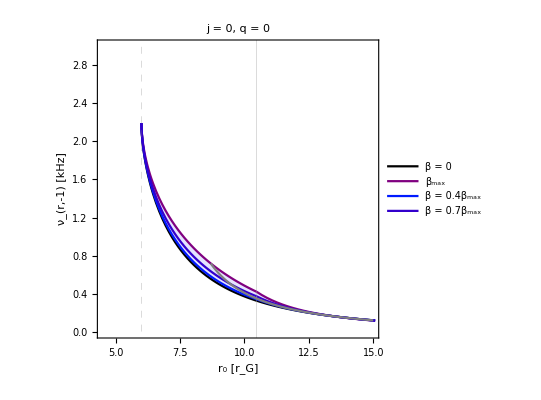

```mathematica
rad1j0q0=Show[Plot[{nur1j0q0b0,nur1j0q0b1},{r0,r1,rm},Frame->True,Axes->False,PlotStyle->{Black,RGBColor[0.5,0,0.5]},PlotRange->{{r1,r2},{0,3}},AspectRatio->1, Filling->{1->{2}},FillingStyle->Directive [Blue,Opacity[0.1]],LabelStyle->16,PlotLabel->Row[{"j = 0, q = 0"}],GridLines->{{{6,Directive[Thick,Dashed]},rm},None},PlotLegends->{"β = 0",Subscript["β","max"]},FrameLabel->{Row[{Subscript[Style["r",FontSlant->Italic],0]," [",Subscript[Style["r",FontSlant->Italic],"G"],"]"}],Row[{Style[Subscript["ν","r,-1"],FontSlant->Italic]," [kHz]"}]}],
ListLinePlot[{nur1j0q0b0tab,nur1j0q0b1tab},PlotStyle->{Black,{color[[4]]}},Filling->{1->{2}},FillingStyle->Directive [Blue,Opacity[0.1]],LabelStyle->16],
Plot[nur1j0q0b04,{r0,r1,rm},PlotStyle->{color[[2]]},LabelStyle->16,PlotLegends->{Row[{"β = 0.4",Subscript["β","max"]}]}],
ListLinePlot[nur1j0q0b04tab,PlotStyle->{{color[[2]]}},LabelStyle->16],
Plot[nur1j0q0b07,{r0,r1,rm},PlotStyle->{color[[3]]},LabelStyle->16,PlotLegends->{Row[{"β = 0.7",Subscript["β","max"]}]}],
ListLinePlot[nur1j0q0b07tab,PlotStyle->{{color[[3]]}},LabelStyle->16],
Plot[nur1j0q0b015,{r0,rb015,r2},PlotStyle->{Gray},LabelStyle->16]]
```

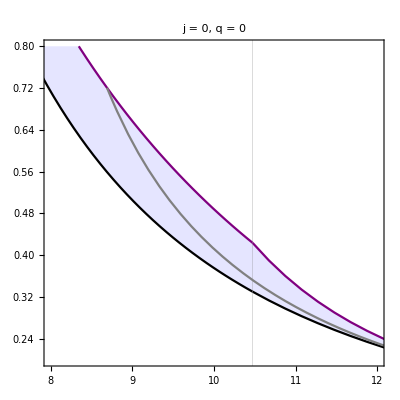

```mathematica
rad1j0q0zoom=Show[Plot[{nur1j0q0b0,nur1j0q0b1},{r0,6.5,rm},Frame->True,Axes->False,PlotStyle->{Black,color[[4]]},PlotRange->{{8,12},{0.2,0.8}},AspectRatio->1, (*FrameTicks->None,*)Filling->{1->{2}},FillingStyle->Directive [Blue,Opacity[0.1]],GridLines->{{{6,Directive[Thick,Dashed]},rm},None},LabelStyle->16,PlotLabel->Row[{"j = 0, q = 0"}]],
ListLinePlot[{nur1j0q0b0tab,nur1j0q0b1tab},PlotStyle->{Black,{color[[4]]}},Filling->{1->{2}},FillingStyle->Directive [Blue,Opacity[0.1]],LabelStyle->16],
Plot[nur1j0q0b015,{r0,rb015,r2},PlotStyle->{Gray},LabelStyle->16]]
```

### Vertical axisymmetric oscillations

```mathematica
Clear[j,q,M,R]
```

```mathematica
c= 2.99792458 10^10 ;    (* speed of light given in [cm/s]  *)
G=6.67428 10^(-8) ;      (* gravitational constant in [cm^3/(g*s^2)] *)

Msun=1.98892 10^(33);    (*solar mass in [g]  *)                   
R=c^3/(G Msun) ;                         (* unit conversion *)
```

```mathematica
color={Black,RGBColor[0,0.1,1],RGBColor[0.2,0,0.8],RGBColor[0.5,0,0.5]}
```

{GrayLevel[0],RGBColor[0, 0.1, 1],RGBColor[0.2, 0, 0.8],RGBColor[0.5, 0, 0.5]}

```mathematica
r1=4.5;r2=15;
```

```mathematica
j=0;q=0;m=0; rm=rmax;
nuh0j0q0b0=νH0/1000;
nuh0j0q0b015=νH/1000/.{β^2->0.15};
nuh0j0q0b04=νH/1000/.{β^2->0.4^2βmax2};
nuh0j0q0b07=νH/1000/.{β^2->0.7^2βmax2}; 
nuh0j0q0b1=νcusph/1000;
nuh0j0q0b04b:=νH/1000/.{β^2->0.4^2βmaxim2}; 
nuh0j0q0b04tab=Table[{r0,nuh0j0q0b04b},{r0,rm,r2+0.5,0.5}];
fcebeta=2/(Ω0^2 A0^2 r0^2)  * (1-ut0/ut)/.{r->rc,h->Pi/2};
fbeta[r0_]=fcebeta-0.15;  abeta=rms; bbeta=rms+10;  cbeta=0.5(abeta+bbeta);countbeta=0; countvalve=100; epsilon=0.000001;
While[Abs[Chop[fbeta[cbeta]]]>epsilon, countbeta=countbeta+1; cbeta=0.5(abeta+bbeta); If[Chop[fbeta[cbeta]]*Chop[fbeta[abeta]]<0,bbeta=cbeta,abeta=cbeta]; If[countbeta>countvalve,{Print["error"],Break[]}]]; rb015=cbeta; Clear[abeta,bbeta,cbeta,countbeta,fbeta];
Clear[j,q,m]
```

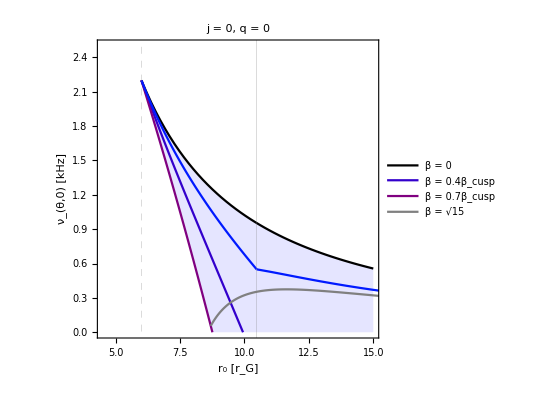

```mathematica
vert0j0q0=Show[Plot[{nuh0j0q0b0,nuh0j0q0b07,nuh0j0q0b1},{r0,6,r2},Frame->True,Axes->False,PlotStyle->{color[[1]],color[[3]],color[[4]]},PlotRange->{{r1,r2},{0,2.5}},AspectRatio->1, Filling->{1->{3}},FillingStyle->Directive [Blue,Opacity[0.1]],LabelStyle->16,PlotLabel->Row[{"j = 0, q = 0"}],GridLines->{{{6,Directive[Thick,Dashed]},rm},None},PlotLegends->{"β = 0",Row[{"β = 0.4",Subscript["β","cusp"]}],Row[{"β = 0.7",Subscript["β","cusp"]}],Subscript["β","cusp"]},FrameLabel->{Row[{Subscript[Style["r",FontSlant->Italic],0]," [",Subscript[Style["r",FontSlant->Italic],"G"],"]"}],Row[{Style[Subscript["ν","θ,0"],FontSlant->Italic]," [kHz]"}]}],
Plot[nuh0j0q0b04,{r0,6.001,rm},PlotStyle->color[[2]]],ListLinePlot[nuh0j0q0b04tab,PlotStyle->color[[2]]],Plot[nuh0j0q0b015,{r0,rb015,20},PlotStyle->{Gray},PlotLegends->{"β = √15"},LabelStyle->16]]
```

### Vertical precession

```mathematica
Clear[j,q,M,R]
```

```mathematica
c= 2.99792458 10^10 ;    (* speed of light given in [cm/s]  *)
G=6.67428 10^(-8) ;      (* gravitational constant in [cm^3/(g*s^2)] *)

Msun=1.98892 10^(33);    (*solar mass in [g]  *)                   
R=c^3/(G Msun) ;                         (* unit conversion *)
```

```mathematica
r1=4.5;r2=15;
```

```mathematica
color={Black,RGBColor[0,0.1,1],RGBColor[0.2,0,0.8],RGBColor[0.5,0,0.5]}
```

{GrayLevel[0],RGBColor[0, 0.1, 1],RGBColor[0.2, 0, 0.8],RGBColor[0.5, 0, 0.5]}

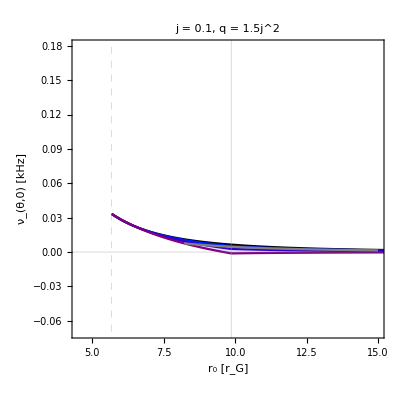

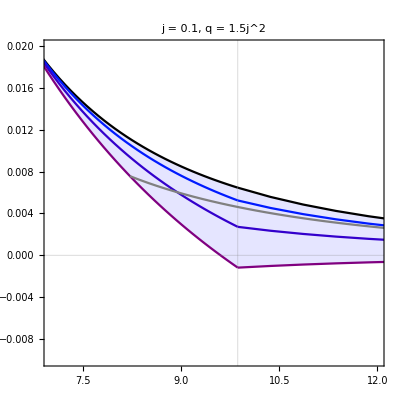

```mathematica
j=0.1;q=1.5j^2;m=-1; rm=rmax;
nuh1b0=-νH0/1000;
nuh1b015=-νH/1000/.{β^2->0.15};
nuh1b04=-νH/1000/.{β^2->0.4^2βmax2};
nuh1b07=-νH/1000/.{β^2->0.7^2βmax2}; 
nuh1b1=-νcusph/1000;
risco=numrms;
nuh1b04b:=-νH/1000/.{β^2->0.4^2βmaxim2};
nuh1b07b:=-νH/1000/.{β^2->0.7^2βmaxim2}; 
nuh1b1b:=-νH/1000/.{β^2->βmaxim2};
nuh1b0tab=Table[{r0,nuh1b0},{r0,rm,r2+0.5,0.5}];
nuh1b04tab=Table[{r0,nuh1b04b},{r0,rm,r2+0.5,0.5}];
nuh1b07tab=Table[{r0,nuh1b07b},{r0,rm,r2+0.5,0.5}];
nuh1b1tab=Table[{r0,nuh1b1b},{r0,rm,r2+0.5,0.5}];
fcebeta=2/(Ω0^2 A0^2 r0^2)  * (1-ut0/ut)/.{r->rc,h->Pi/2};
fbeta[r0_]=fcebeta-0.15;  abeta=rms; bbeta=rms+10;  cbeta=0.5(abeta+bbeta);countbeta=0; countvalve=100; epsilon=0.000001;
While[Abs[Chop[fbeta[cbeta]]]>epsilon, countbeta=countbeta+1; cbeta=0.5(abeta+bbeta); If[Chop[fbeta[cbeta]]*Chop[fbeta[abeta]]<0,bbeta=cbeta,abeta=cbeta]; If[countbeta>countvalve,{Print["error"],Break[]}]]; r015=cbeta; Clear[abeta,bbeta,cbeta,countbeta,fbeta];
vert11=Show[Plot[{nuh1b0,nuh1b04,nuh1b07,nuh1b1},{r0,risco+0.01,rm},Frame->True,Axes->False,PlotStyle->color,PlotRange->{{r1,r2},{-0.07,0.18}},AspectRatio->1,GridLines->{{{risco,Directive[Thick,Dashed]},rm},{0}}, Filling->{1->{4}},FillingStyle->Directive [Blue,Opacity[0.1]],LabelStyle->16,PlotLabel->Row[{"j = ",j,", q = ",q/j^2,"j^2"}],FrameLabel->{Row[{Subscript[Style["r",FontSlant->Italic],0]," [",Subscript[Style["r",FontSlant->Italic],"G"],"]"}],Row[{Style[Subscript["ν","θ,0"],FontSlant->Italic]," [kHz]"}]}],
ListLinePlot[{nuh1b0tab,nuh1b1tab},PlotStyle->{Black,{color[[4]]}},Filling->{1->{2}},FillingStyle->Directive [Blue,Opacity[0.1]],LabelStyle->16],
ListLinePlot[nuh1b04tab,PlotStyle->{{color[[2]]}},LabelStyle->16],ListLinePlot[nuh1b07tab,PlotStyle->{color[[3]]},LabelStyle->16],Plot[nuh1b015,{r0,r015,r2},PlotStyle->{Gray},LabelStyle->16]]
vert11zoom=Show[Plot[{nuh1b0,nuh1b04,nuh1b07,nuh1b1},{r0,risco+0.01,rm},Frame->True,Axes->False,PlotStyle->color,PlotRange->{{7,12},{-0.01,0.02}},AspectRatio->1,FrameTicks->None,GridLines->{{{risco,Directive[Thick,Dashed]},rm},{0}}, Filling->{1->{4}},FillingStyle->Directive [Blue,Opacity[0.1]],LabelStyle->16,PlotLabel->Row[{"j = ",j,", q = ",q/j^2,"j^2"}]],ListLinePlot[{nuh1b0tab,nuh1b1tab},PlotStyle->{Black,{color[[4]]}},Filling->{1->{2}},FillingStyle->Directive [Blue,Opacity[0.1]],LabelStyle->16],
ListLinePlot[nuh1b04tab,PlotStyle->{{color[[2]]}},LabelStyle->16],ListLinePlot[nuh1b07tab,PlotStyle->{color[[3]]},LabelStyle->16],Plot[nuh1b015,{r0,r015,r2},PlotStyle->{Gray},LabelStyle->16]]
Clear[j,q,m]
```

### Approximate relations

```mathematica
M=1;c= 2.99792458 10^10 ;G=6.67428 10^(-8) ; Msun=1.98892 10^(33)  ;R=c^3/(G Msun);
```

```mathematica
rkep=((6^1.5- j nuk/nu0 +0.5(q-j^2)(nuk/nu0 )^2)/(nuk/nu0))^(2/3);nu0=1/(2Pi)R/6^(3/2);
```

```mathematica
radaxisym=nuk b1 Sqrt[1-6/r0+8j/r0^(3/2) +57j^2/r0^(7/2)-3q/r0^2 (1+19/r0^(3/2))]/.r0->rkep;
radprec=nuk(1-b2 Sqrt[1-6/r0+8j/r0^(3/2) +57j^2/r0^(7/2)-3q/r0^2 (1+19/r0^(3/2))])/.r0->rkep;
vertaxisym=nuk b3 Sqrt[1-4j/r0^(3/2)-24j^2/r0^(7/2)+3q /r0^2(1+8/r0^(3/2)) ]/.r0->rkep;
vertprec=nuk(1-b4 Sqrt[1-4j/r0^(3/2)-24j^2/r0^(7/2)+3q /r0^2(1+8/r0^(3/2)) ])/.r0->rkep;
```

```mathematica
b1=1-b^2 (1/33+10/nu0(r0^1.5-18.4+15j-4q)^2/(1-1.5j+0.6q))/.r0->rkep;
b2=1-0.2b^2 (1+j);
b3=1-b^2 (14/nu0(r0^1.5-40/3+10j-2.5q)^2/(1-1.7j+0.7q))/.r0->rkep;
b4=1-b^2(5j/nu0(1-2/(1-2j-2 j^2 +3q)(r0-6.1+2.5 j)^2)+9(q-j^2)/nu0 (r0-7.2))/.r0->rkep;
```

```mathematica
color={RGBColor[0,0,1],RGBColor[0.2,0,0.8],RGBColor[0.5,0,0.5]}
```

{RGBColor[0, 0, 1],RGBColor[0.2, 0, 0.8],RGBColor[0.5, 0, 0.5]}

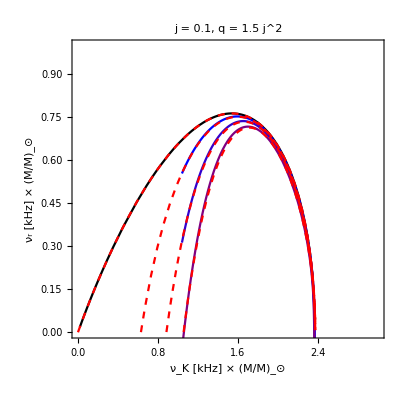
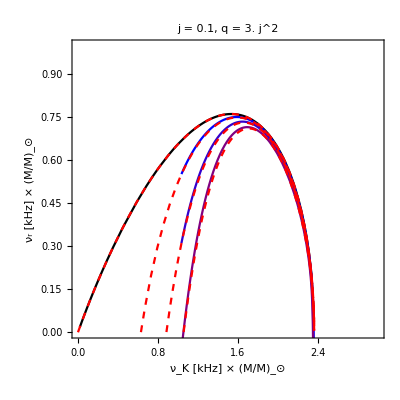
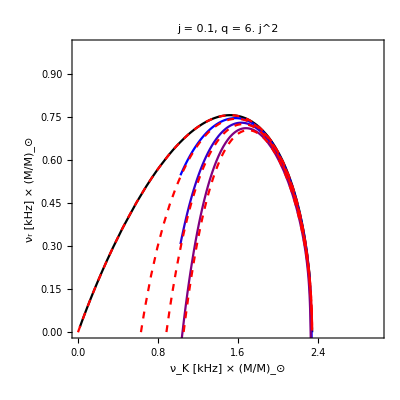
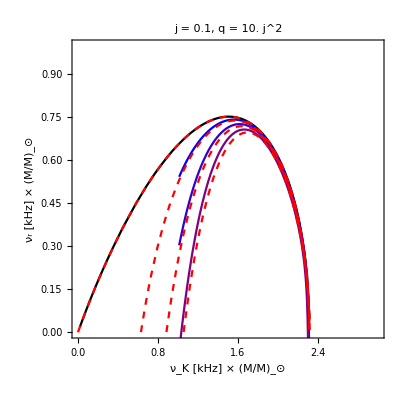
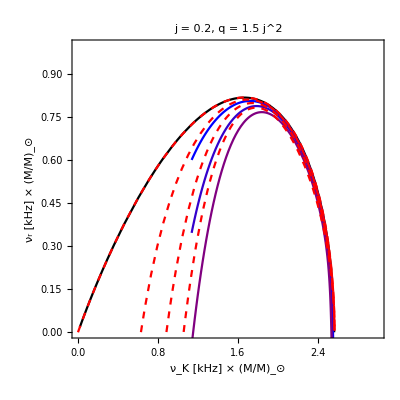
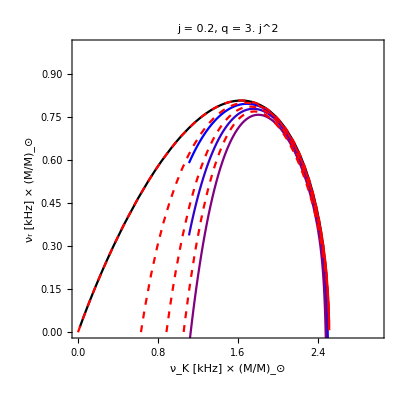
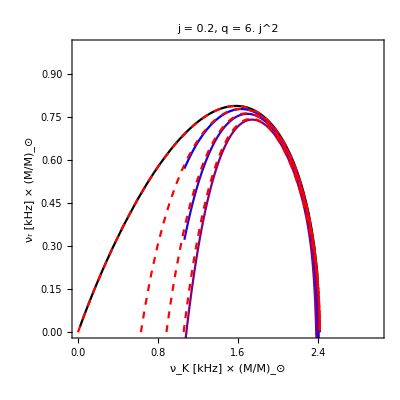
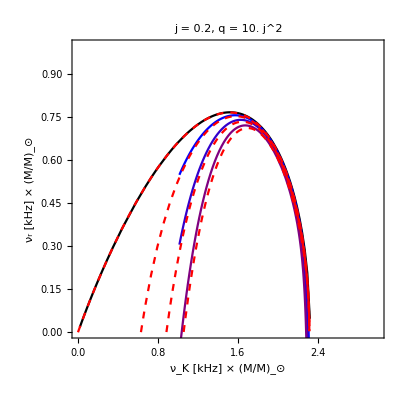

```mathematica
je={0.1,0.2,0.35};  qe={1.5,3,6,10}j^2;m=0; radm0pl=Table[None,{i,1,3},{k,1,4}];
For[x=1,x<=3,x++,j=je[[x]];
For[y=1,y<=4,y++,q=qe[[y]]; 
nukep=νK/1000;
nub0=νR0/1000;
nub04=νR/1000/.{β^2->0.4^2βmax2};
nub07=νR/1000/.{β^2->0.7^2βmax2}; 
nub1=νcuspr/1000;
risco=numrms;
rm=rmax;
radm0pl[[x]][[y]]=Show[ParametricPlot[{nukep,nub0},{r0,risco,150},PlotStyle->Black,Frame->True,PlotLabel->Row[{"j = ", j, ", q = ", q/j^2," j^2"}],AspectRatio->1,PlotRange->{{0,3},{0,1}},FrameLabel->{Row[{Subscript["ν","K"]," [kHz] × ",Subscript[Style["M/M",FontSlant->Italic],"⊙"]}],Row[{Subscript["ν","r"]," [kHz] × ",Subscript[Style["M/M",FontSlant->Italic],"⊙"]}]}],
ParametricPlot[{{nukep,nub04},{nukep,nub07},{nukep,nub1}},{r0,risco,rm},PlotStyle->color],
Plot[{radaxisym/1000/.b->0/.nuk->1000nu,radaxisym/1000/.b->0.4/.nuk->1000nu,radaxisym/1000/.b->0.7/.nuk->1000nu,radaxisym/1000/.b->1/.nuk->1000nu },{nu,0,3},PlotStyle->{{Red,Dashed}}]]
]]
Clear[j,q,x,y,je,qe]
radm0pl
```

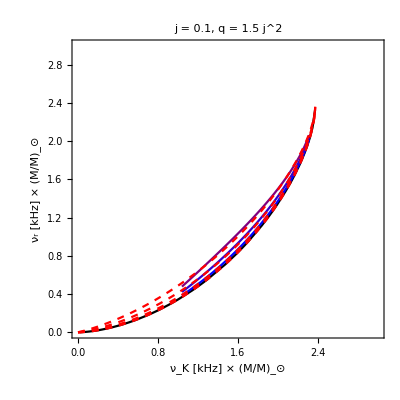
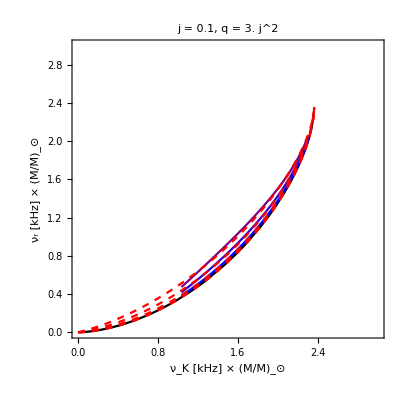
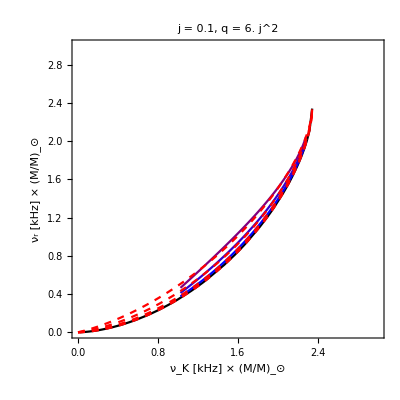
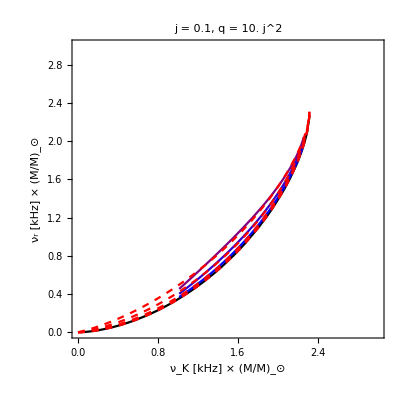
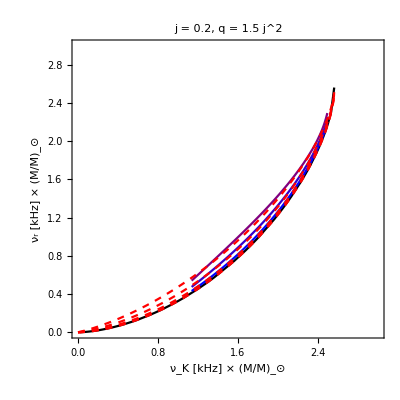
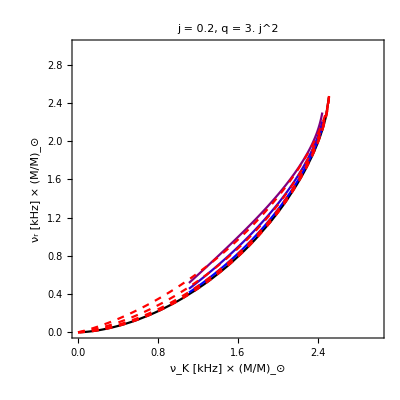
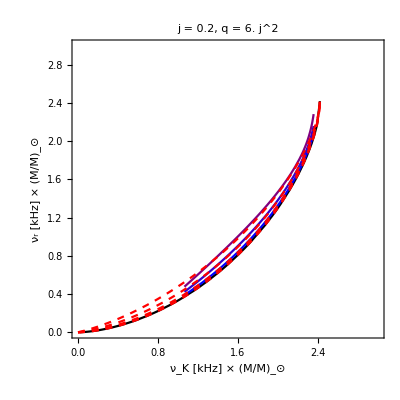
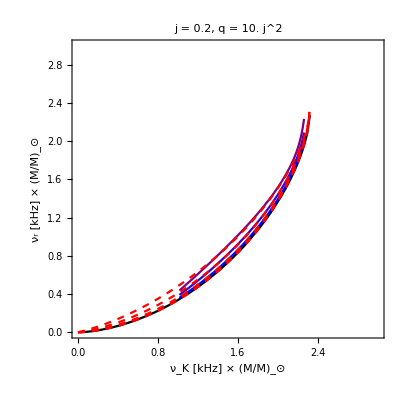

```mathematica
je={0.1,0.2,0.35};  qe={1.5,3,6,10}j^2;m=-1; radm1pl=Table[None,{i,1,3},{k,1,4}];
For[x=1,x<=3,x++,j=je[[x]];
For[y=1,y<=4,y++,q=qe[[y]]; 
nukep=νK/1000;
nub0=-νR0/1000;
nub04=-νR/1000/.{β^2->0.4^2βmax2};
nub07=-νR/1000/.{β^2->0.7^2βmax2}; 
nub1=-νcuspr/1000;
risco=numrms;numax=nukep/.r0->risco;
rm=rmax;
radm1pl[[x]][[y]]=Show[ParametricPlot[{nukep,nub0},{r0,risco,150},PlotStyle->Black,Frame->True,PlotLabel->Row[{"j = ", j, ", q = ", q/j^2," j^2"}],AspectRatio->1,PlotRange->{0,3},(*PlotRange->{{1.4,2.2},{0.8,1.8}},FrameTicks->None,*)FrameLabel->{Row[{Subscript["ν","K"]," [kHz] × ",Subscript[Style["M/M",FontSlant->Italic],"⊙"]}],Row[{Subscript["ν","r"]," [kHz] × ",Subscript[Style["M/M",FontSlant->Italic],"⊙"]}]}],
ParametricPlot[{{nukep,nub04},{nukep,nub07},{nukep,nub1}},{r0,risco+0.1,rm},PlotStyle->color],
Plot[{radprec/1000/.b->0/.nuk->1000nu,radprec/1000/.b->0.4/.nuk->1000nu,radprec/1000/.b->0.7/.nuk->1000nu,radprec/1000/.b->1/.nuk->1000nu },{nu,0,numax},PlotStyle->{{Red,Dashed}}]]
]]
Clear[j,q,x,y,je,qe]
radm1pl
```

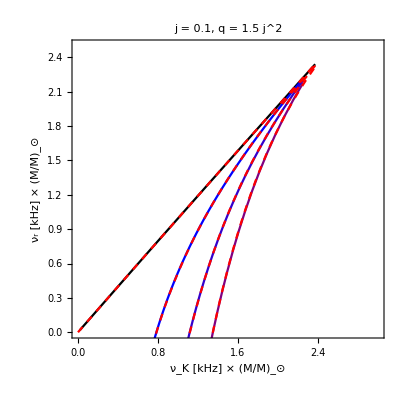
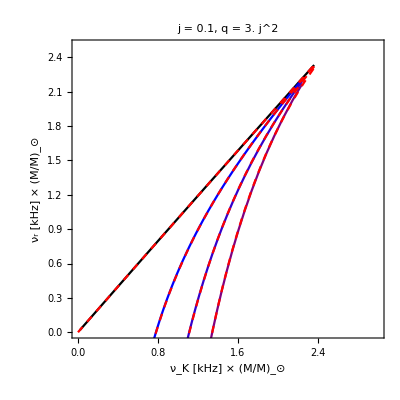
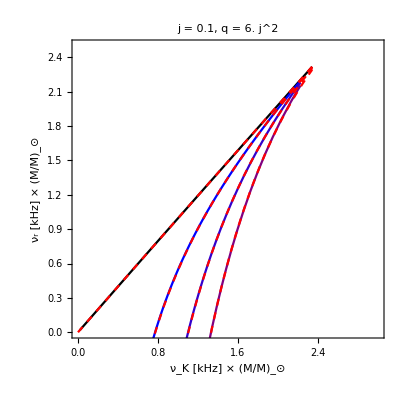
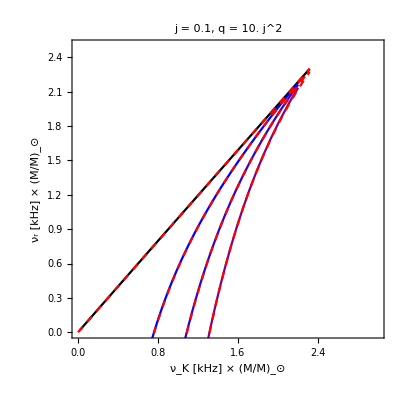
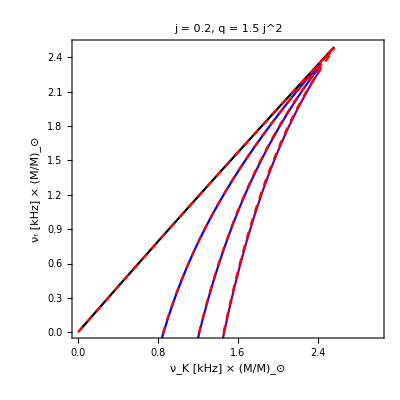
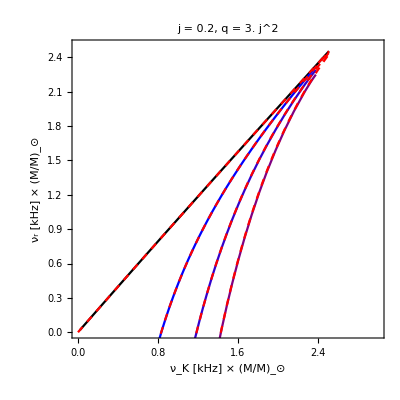
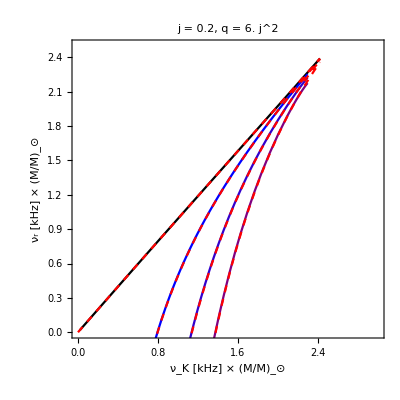
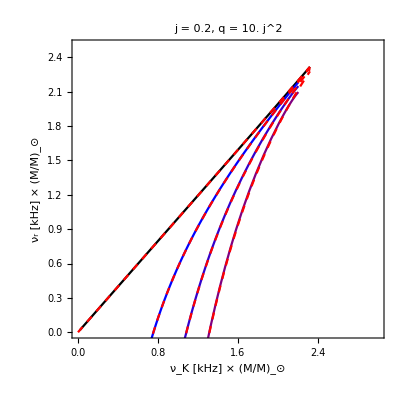

```mathematica
je={0.1,0.2,0.35};  qe={1.5,3,6,10}j^2;m=0; vertm0pl=Table[None,{i,1,3},{k,1,4}];
For[x=1,x<=3,x++,j=je[[x]];
For[y=1,y<=4,y++,q=qe[[y]]; 
nukep=νK/1000;
nub0=νH0/1000;
nub04=νH/1000/.{β^2->0.4^2βmax2};
nub07=νH/1000/.{β^2->0.7^2βmax2}; 
nub1=νcusph/1000;
risco=numrms;numax=nukep/.r0->risco;
vertm0pl[[x]][[y]]=Show[ParametricPlot[{nukep,nub0},{r0,risco,150},PlotStyle->Black,Frame->True,PlotLabel->Row[{"j = ", j, ", q = ", q/j^2," j^2"}],AspectRatio->1,PlotRange->{{0,3},{0,2.5}},FrameLabel->{Row[{Subscript["ν","K"]," [kHz] × ",Subscript[Style["M/M",FontSlant->Italic],"⊙"]}],Row[{Subscript["ν","r"]," [kHz] × ",Subscript[Style["M/M",FontSlant->Italic],"⊙"]}]}],
ParametricPlot[{{nukep,nub04},{nukep,nub07},{nukep,nub1}},{r0,risco+0.2,15},PlotStyle->color],
Plot[{vertaxisym/1000/.b->0/.nuk->1000nu,vertaxisym/1000/.b->0.4/.nuk->1000nu,vertaxisym/1000/.b->0.7/.nuk->1000nu,vertaxisym/1000/.b->1/.nuk->1000nu },{nu,0,numax},PlotStyle->{{Red,Dashed}}]]
]]
Clear[j,q,x,y,je,qe]
vertm0pl
```

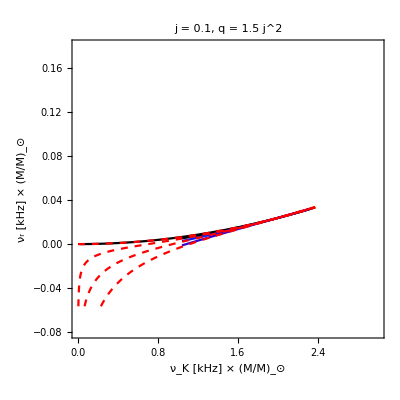
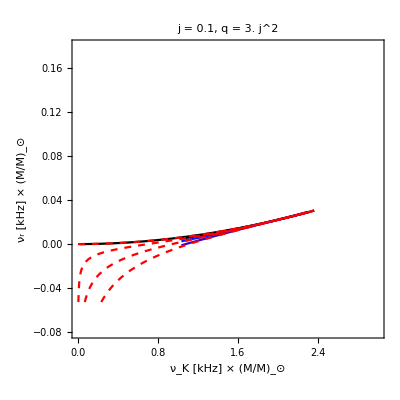
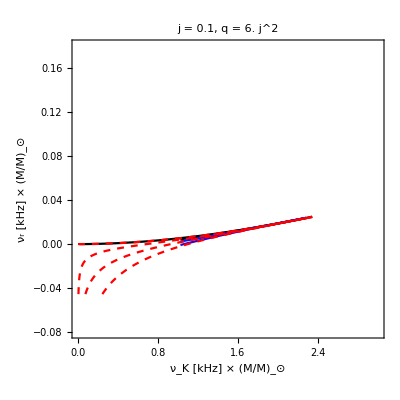
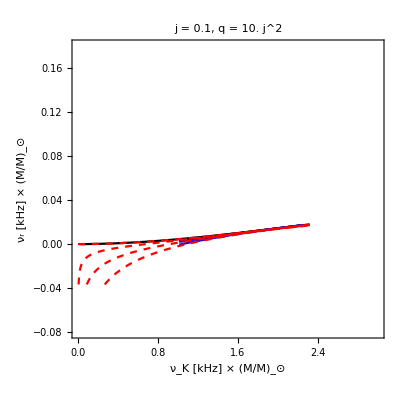
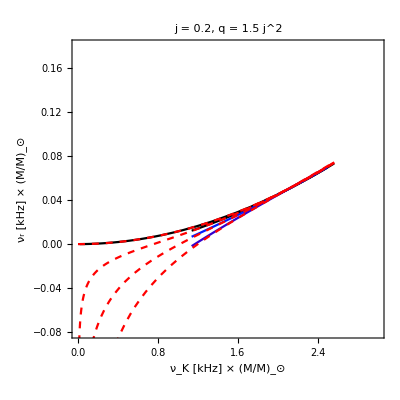
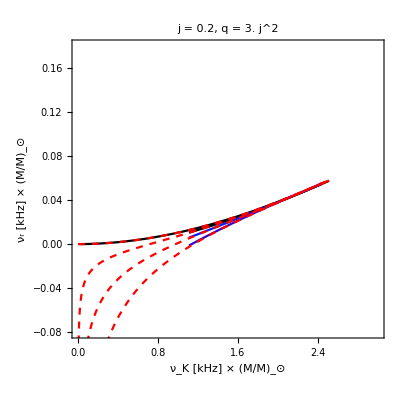
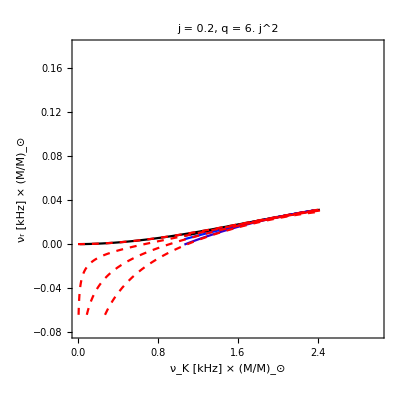
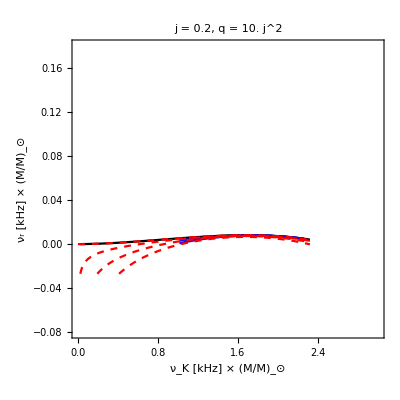

```mathematica
je={0.1,0.2,0.35};  qe={1.5,3,6,10}j^2;m=-1; vertm1pl=Table[None,{i,1,3},{k,1,4}];
For[x=1,x<=3,x++,j=je[[x]];
For[y=1,y<=4,y++,q=qe[[y]]; 
nukep=νK/1000;
nub0=-νH0/1000;
nub04=-νH/1000/.{β^2->0.4^2βmax2};
nub07=-νH/1000/.{β^2->0.7^2βmax2}; 
nub1=-νcusph/1000;
risco=numrms;numax=nukep/.r0->risco;
rm=rmax;
vertm1pl[[x]][[y]]=Show[ParametricPlot[{nukep,nub0},{r0,risco,150},PlotStyle->Black,Frame->True,PlotLabel->Row[{"j = ", j, ", q = ", q/j^2," j^2"}],AspectRatio->1,(*PlotRange->{{1,1.7},{0,0.04}},*)PlotRange->{{0,3},{-0.08,0.18}},(*FrameTicks->None,*)FrameLabel->{Row[{Subscript["ν","K"]," [kHz] × ",Subscript[Style["M/M",FontSlant->Italic],"⊙"]}],Row[{Subscript["ν","r"]," [kHz] × ",Subscript[Style["M/M",FontSlant->Italic],"⊙"]}]}],
ParametricPlot[{{nukep,nub04},{nukep,nub07},{nukep,nub1}},{r0,risco+0.1,rm},PlotStyle->color],
Plot[{vertprec/1000/.b->0/.nuk->1000nu,vertprec/1000/.b->0.4/.nuk->1000nu,vertprec/1000/.b->0.7/.nuk->1000nu,vertprec/1000/.b->1/.nuk->1000nu },{nu,0,numax},PlotStyle->{{Red,Dashed}}]]
]]
Clear[j,q,x,y,je,qe]
vertm1pl
```